```mathematica
SetDirectory[NotebookDirectory[]]
FileNames[]
```

/Users/lamont/Dropbox/Colin_ControlTheory/HIV trapping code/BloomAntibodies

{10E8-60ug-rep1_mutfracsurvive.csv,10E8-60ug-rep1_sitefracsurvive.csv,10E8-median_fracsurvive.pdf,Ab_subset_median_avgsitefracsurvive.pdf,Untitled-5.nb}

```mathematica
sitevec=Drop[Import["10E8-60ug-rep1_sitefracsurvive.csv"],{1}];
```

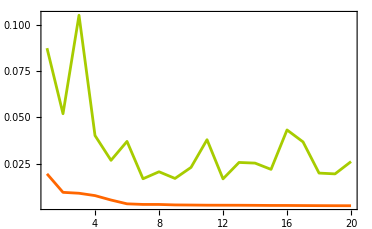

```mathematica
ListPlot[{sitevec[[;;20,2]],sitevec[[;;20,3]]},PlotRange->All,Joined->True]
```

```mathematica
mutvec=Drop[Import["10E8-60ug-rep1_mutfracsurvive.csv"],{1}];
```

```mathematica
Dimensions[mutvec]
```

{13400,4}

```mathematica
sitevec[[;;10,1]]
```

{671,672,683,673,676,365,643,618,474,80}

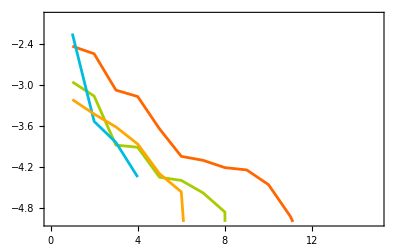

```mathematica
ListPlot[Log@Table[Cases[mutvec,{ii,___}][[;;,4]],{ii,sitevec[[;;4,1]]}],Joined->True,PlotRange->{-5,-2}]
```

```mathematica
mutlist10e8=Table[({#[[1,1]],
DeleteDuplicates[#[[;;,2]]],
DeleteDuplicates[#[[;;,3]]]
})&@Cases[mutvec,{ii,a_,b_,c_/;Log[c]>-5}],{ii,sitevec[[;;4,1]]}]
```

{{671,{N},{T,L,F,R,V,Y,C,K,Q,M,I}},{672,{W},{V,G,E,D,F,L,R,C}},{683,{K},{Y,H,Q,W}},{673,{F},{R,A,L,V,C,S}}}